```mathematica
aa=d x - I d y;
bb=R y - d R + I R x;
dd = R y- d R - I R x;
ee = d x+I d y;
cata=y/.Solve[256aa^3ee^3-192aa^2bb dd ee^2-27aa^2dd^4-6aa bb^2dd^2ee-27bb^4ee^2-4bb^3dd^3==0,y];
```

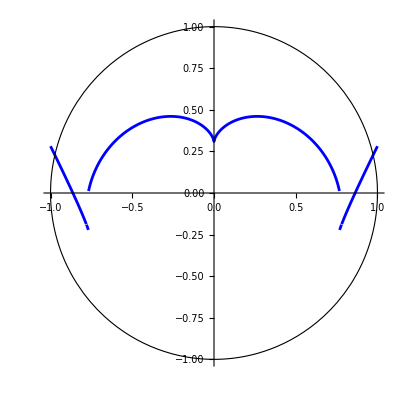

```mathematica
R=1;d=80/100;
Plot[{cata,√(1-x^2),-√(1-x^2)},{x,-1,1},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->{{Thickness[.005],Blue},{Thickness[.002],Black},{Thickness[.002],Black}}]
```

```mathematica
For[i=1,i<101,i++,
R=1;
d=i/100;
Export[
StringJoin[ToString[i],".png"],
Plot[{cata,√(1-x^2),-√(1-x^2)},{x,-1,1},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->{{Thickness[.005],Blue},{Thickness[.002],Black},{Thickness[.002],Black}}]
];
Print[i]
]
```